```mathematica
Define the dispersion relation
```

```mathematica
EE[a_,b_,kx_,ky_]:=-2(Cos[kx a]+Cos[ky b]);
```

```mathematica
F[A_,B_]:=EE[1,1,A,B]
```

### Built a vector to store the states number

```mathematica
Array[Eee,200]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,31,49,56,62,63,64,69,70,73,71,69,81,67,69,86,83,72,89,75,81,83,81,85,85,91,83,86,87,89,97,87,84,101,99,89,99,95,102,101,95,101,92,111,109,105,111,109,112,115,103,119,115,116,127,121,119,125,129,133,139,125,121,148,155,150,145,143,153,165,167,159,170,167,200,203,200,196,229,271,318,312,264,222,224,222,220,184,190,172,182,180,168,158,160,166,168,158,132,136,150,144,142,136,132,134,140,122,124,130,116,128,122,116,122,116,122,124,96,110,108,114,112,102,108,102,112,114,88,98,108,102,100,94,92,102,96,98,94,96,94,88,102,82,96,102,82,80,94,82,86,90,90,86,86,82,86,84,86,86,52,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
nn=1;While[nn<201,Eee[nn]=0;nn++]
```

### Calculate the how many states in one small energy interval.

```mathematica
(*-------- Original --------*)
For[i=0,i<=200,i++,
For[j=0,j≤200,j++,
{
n=1;
While[n<201,{
If[F[i Pi/100-Pi,j Pi/100-Pi]≥(n/25-4)&&F[i Pi/100-Pi,j Pi/100-Pi]<((n+1)/25-4),Eee[n]++]
};
n++]
}
]
]
```

$Aborted

```mathematica
(*-------- Improved by YLL --------*)
For[i=0,i<=200,i++,
For[j=0,j≤200,j++,
{
energy=F[i Pi/100-Pi,j Pi/100-Pi]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy,{-5,5},{0,200}]//Round;    (* find appropriate bin *)
Eee[n]++
}
]
]
```

### Plot

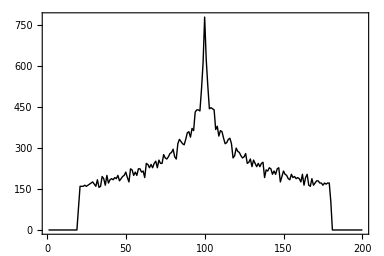

```mathematica
ListPlot[Table[{i,Eee[i]},{i,0,200}]]
```

### Smooth plot (average the five nearby states)

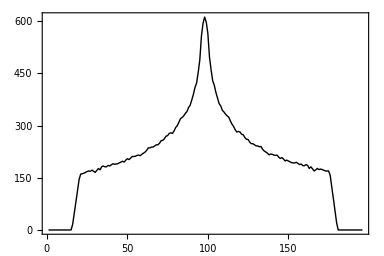

```mathematica
ListPlot[Table[{i,(Eee[i]+Eee[i+1]+Eee[i+2]+Eee[i+3]+Eee[i+4])/5},{i,0,200}]]
```